```mathematica
2+2
```

4

# The calculator

```mathematica
Plus[2,2]
```

4

```mathematica
13-7
```

6

```mathematica
Plus[13,-7]
```

6

```mathematica
Subtract[13,7]
```

6

```mathematica
a+b
```

a+b

```mathematica
Times[2,6]
```

12

```mathematica
12/7
```

12/7

```mathematica
N[12/7]
```

1.71429

```mathematica
NumberForm[1.7142857142857142,10]
```

1.714285714

```mathematica
Divide[12,7]
```

12/7

```mathematica
Power[6,3]
```

216

```mathematica
6^3
```

216

```mathematica
Sqrt[36]
```

6

```mathematica
N[1/6^3]
```

0.00462963

```mathematica
FullForm[ab+xy]
```

Plus[ab,xy]

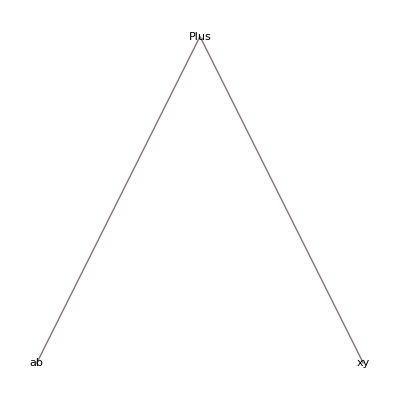

```mathematica
TreeForm[ab+xy]
```

```mathematica
√□
```

√□

```mathematica
√2
```

√2

```mathematica
27^(1/3)
```

3

```mathematica
81^(1/4)
```

3

```mathematica
Sin[Pi/6]
```

1/2

```mathematica
ⅇ^3
```

ⅇ^3

```mathematica
Sin[Π/3]
```

Sin[Π/3]

```mathematica
N[Cos[Π/6]]
```

Cos[0.166667 Π]

```mathematica
FindMinimum[Cos[Π/6],{{Π,3.14}}]
```

{-1.,{Π→56.5487}}

```mathematica
Cos[Π/2]
```

```mathematica
Cos[Π/2]
```

Cos[Π/2]

```mathematica
Sin[π/6]
```

1/2

```mathematica
Log[10,100]
```

2

```mathematica
GCD[15,5]
```

5

# Collections

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
myList={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
myList
```

{1,2,3,4,5}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[1,5]
```

{1,2,3,4,5}

```mathematica
Range[2,20,2]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Range[10,1,-1]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Table[n,{n,1,10,1}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[2*n,{n,1,10,1}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[n^2,{n,1,6,1}]
```

{1,4,9,16,25,36}

```mathematica
Table[{a,b},{a,10,12},{b,13,15}]
```

{{{10,13},{10,14},{10,15}},{{11,13},{11,14},{11,15}},{{12,13},{12,14},{12,15}}}

```mathematica
Table[i+j,{i,1,3},{j,5,7}]
```

{{6,7,8},{7,8,9},{8,9,10}}

```mathematica
myList
```

{1,2,3,4,5}

```mathematica
Reverse[myList]
```

{5,4,3,2,1}

```mathematica
myList
```

{1,2,3,4,5}

```mathematica
Append[myList,6]
```

{1,2,3,4,5,6}

```mathematica
myList
```

{1,2,3,4,5}

```mathematica
Drop[myList,2]
```

{3,4,5}

```mathematica
myList=Append[myList,6]
```

{1,2,3,4,5,6}

```mathematica
myList
```

{1,2,3,4,5,6}

```mathematica
Join[{1,2,3,4,5},{6,7,8,9,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
3*myList
```

{3,6,9,12,15,18}

```mathematica
{4,5,8}*{11,12,13}
```

{44,60,104}

```mathematica
Length[myList]
```

6

```mathematica
Length[{{2,3},{7,8},{9,11},{78,79},{85,889}}]
```

5

```mathematica
Dimensions[{{2,3},{7,8},{9,11},{78,79},{85,889}}]
```

{5,2}

```mathematica
Min[myList]
```

1

```mathematica
Max[myList]
```

6

```mathematica
Sort[{11,87,6,12,88,56,2}]
```

{2,6,11,12,56,87,88}

```mathematica
Part[{78,79,47,58},1]
```

78

```mathematica
myList[[0]]
```

List

```mathematica
myList[0]
```

{1,2,3,4,5,6}[0]

```mathematica
{2,9,7,6,8,7,15,23}[0]
```

{2,9,7,6,8,7,15,23}[0]

```mathematica
{2,9,7,6,8,7,15,23}[[0]]
```

List

```mathematica
{2,9,7,6,8,7,15,23}[ [0]]
```

List

```mathematica
{2,9,7,6,8,7,15,23}[[1]]
```

2

```mathematica
myList[4]
```

{1,2,3,4,5,6}[4]

```mathematica
myList[[4]]
```

4

```mathematica
M={{x,y,z},{a,b,c},{p,q,r}}
```

{{x,y,z},{a,b,c},{p,q,r}}

```mathematica
M[[2]]
```

{a,b,c}

```mathematica
M[[2,1]]
```

a

```mathematica
Count[myList]
```

Count[{1,2,3,4,5,6}]

```mathematica
Count[myList,1]
```

1

```mathematica
K={2,7,8,2,3,1,4,4,5,1,3,8,9,7}
```

{2,7,8,2,3,1,4,4,5,1,3,8,9,7}

```mathematica
Counts[K]
```

<|2→2,7→2,8→2,3→2,1→2,4→2,5→1,9→1|>

```mathematica
Thread[{a,b,c}-> {1,2,3}]
```

{a→1,b→2,c→3}

```mathematica
Partition[{a,b,c,d,e,f,g},2]
```

{{a,b},{c,d},{e,f}}

```mathematica
Flatten[{{a,b,c},{d,e,f},{p,q,r}}]
```

{a,b,c,d,e,f,p,q,r}

```mathematica
Gather[{1,4,3,4,5,4,3,4,5,6,3,5,5,4,6,3,88,7,6,9,8,9}]
```

{{1},{4,4,4,4,4},{3,3,3,3},{5,5,5,5},{6,6,6},{88},{7},{9,9},{8}}

```mathematica
Sort[Gather[{1,4,3,4,5,4,3,4,5,6,3,5,5,4,6,3,88,7,6,9,8,9}]]
```

{{1},{7},{8},{88},{9,9},{6,6,6},{3,3,3,3},{5,5,5,5},{4,4,4,4,4}}

```mathematica
Union[{2,1,2,3,2,4},{2,3,8,9,10}]
```

{1,2,3,4,8,9,10}

```mathematica
Intersection[{2,1,2,3,2,4},{2,3,8,9,10}]
```

{2,3}

```mathematica
Complement[{2,1,2,3,2,4},{1,2,3}]
```

{4}

```mathematica
Riffle[{45,60,65,15,85,95,40},55]
```

{45,55,60,55,65,55,15,55,85,55,95,55,40}

```mathematica
Permutations[{a,b,c}]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

```mathematica
Subsets[{2,5,6}]
```

{{},{2},{5},{6},{2,5},{2,6},{5,6},{2,5,6}}

```mathematica
Tuples[{1,2,3,4,5,6},3]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{2,5,6},{2,6,1},{2,6,2},{2,6,3},{2,6,4},{2,6,5},{2,6,6},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,1,6},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,4,6},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{3,5,6},{3,6,1},{3,6,2},{3,6,3},{3,6,4},{3,6,5},{3,6,6},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,1,6},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,3,6},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,4,6},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{4,5,6},{4,6,1},{4,6,2},{4,6,3},{4,6,4},{4,6,5},{4,6,6},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,1,6},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,2,6},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,3,6},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,4,6},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{5,5,6},{5,6,1},{5,6,2},{5,6,3},{5,6,4},{5,6,5},{5,6,6},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{6,3,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{6,3,6},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,4,5},{6,4,6},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,5,6},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6}}

```mathematica
Table[1,4,5]
```

{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}

```mathematica
Grid[Table[n,3,4]]
```

n | n | n | n
n | n | n | n
n | n | n | n

```mathematica
Red
```

RGBColor[1, 0, 0]

```mathematica
RGBColor[1,0,0]
```

RGBColor[1, 0, 0]

```mathematica
Table[RGBColor[r,1,1],{r,0,1,0.05}]
```

{RGBColor[0., 1, 1],RGBColor[0.05, 1, 1],RGBColor[0.1, 1, 1],RGBColor[0.15000000000000002, 1, 1],RGBColor[0.2, 1, 1],RGBColor[0.25, 1, 1],RGBColor[0.30000000000000004, 1, 1],RGBColor[0.35000000000000003, 1, 1],RGBColor[0.4, 1, 1],RGBColor[0.45, 1, 1],RGBColor[0.5, 1, 1],RGBColor[0.55, 1, 1],RGBColor[0.6000000000000001, 1, 1],RGBColor[0.65, 1, 1],RGBColor[0.7000000000000001, 1, 1],RGBColor[0.75, 1, 1],RGBColor[0.8, 1, 1],RGBColor[0.8500000000000001, 1, 1],RGBColor[0.9, 1, 1],RGBColor[0.9500000000000001, 1, 1],RGBColor[1., 1, 1]}

```mathematica
Grid[Table[RGBColor[r,g,0],{r,0,1,0.2},{g,0,1,0.2}]]
```

RGBColor[0., 0., 0] | RGBColor[0., 0.2, 0] | RGBColor[0., 0.4, 0] | RGBColor[0., 0.6000000000000001, 0] | RGBColor[0., 0.8, 0] | RGBColor[0., 1., 0]
RGBColor[0.2, 0., 0] | RGBColor[0.2, 0.2, 0] | RGBColor[0.2, 0.4, 0] | RGBColor[0.2, 0.6000000000000001, 0] | RGBColor[0.2, 0.8, 0] | RGBColor[0.2, 1., 0]
RGBColor[0.4, 0., 0] | RGBColor[0.4, 0.2, 0] | RGBColor[0.4, 0.4, 0] | RGBColor[0.4, 0.6000000000000001, 0] | RGBColor[0.4, 0.8, 0] | RGBColor[0.4, 1., 0]
RGBColor[0.6000000000000001, 0., 0] | RGBColor[0.6000000000000001, 0.2, 0] | RGBColor[0.6000000000000001, 0.4, 0] | RGBColor[0.6000000000000001, 0.6000000000000001, 0] | RGBColor[0.6000000000000001, 0.8, 0] | RGBColor[0.6000000000000001, 1., 0]
RGBColor[0.8, 0., 0] | RGBColor[0.8, 0.2, 0] | RGBColor[0.8, 0.4, 0] | RGBColor[0.8, 0.6000000000000001, 0] | RGBColor[0.8, 0.8, 0] | RGBColor[0.8, 1., 0]
RGBColor[1., 0., 0] | RGBColor[1., 0.2, 0] | RGBColor[1., 0.4, 0] | RGBColor[1., 0.6000000000000001, 0] | RGBColor[1., 0.8, 0] | RGBColor[1., 1., 0]

# Algebra

```mathematica
Solve[x^2-2x-8==0,x]
```

{{x→-2},{x→4}}

```mathematica
Solve[ax^2+bx+c==0,x]
```

{}

```mathematica
Solve[ax^2+bx+c==0,x]
```

{}

```mathematica
Solve[ax^2+bx+c==0,x]
```

{}

```mathematica
First[{}]
```

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
Solve[2x+8==0,x]
```

{{x→-4}}

```mathematica
x/.{{x->-4}}
```

{-4}

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[a*x+y==7&&b*x-y==1,{x,y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

```mathematica
solution=Solve[x^2+y^2==25&&x-y==1,{x,y}]
```

{{x→-3,y→-4},{x→4,y→3}}

```mathematica
solution
```

{{x→-3,y→-4},{x→4,y→3}}

```mathematica
x^2+y^2==25&&x-y==1/.solution
```

{True,True}

```mathematica
Solve[x^8-5*x^4+4==0,x]
```

{{x→-1},{x→-ⅈ},{x→ⅈ},{x→1},{x→-√2},{x→-ⅈ √2},{x→ⅈ √2},{x→√2}}

```mathematica
Solve[x^8-5*x^4+4==0,x,Reals]
```

{{x→-1},{x→1},{x→-√2},{x→√2}}

```mathematica
Solve[x^8-5*x^4+4==0&&x>0,x,Reals]
```

{{x→1},{x→√2}}

```mathematica
Solve[x^8-5*x^4+4==0,x,Integers]
```

{{x→-1},{x→1}}

```mathematica
Solve[a*x^2+b*x+c==0,x,Reals]
```

{{x→ConditionalExpression[-b/(2 a)-1/2 √((b^2-4 a c)/a^2), ]},{x→ConditionalExpression[-b/(2 a)+1/2 √((b^2-4 a c)/a^2), ]}}

```mathematica
Solve[Sin[θ]==1/2,θ]
```

{{θ→ConditionalExpression[π/6+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[(5 π)/6+2 π C[1], C[1]∈ℤ]}}

ⅇ^x+sinx

```mathematica
FindRoot[ⅇ^x+Sin[x],{x,0}]
```

{x→-0.588533}

```mathematica
NSolve[x^5-2*x+3==0,x]
```

{{x→-1.42361},{x→-0.246729-1.32082 ⅈ},{x→-0.246729+1.32082 ⅈ},{x→0.958532-0.498428 ⅈ},{x→0.958532+0.498428 ⅈ}}

```mathematica
Clear[x]
```

```mathematica
VectorQ[{1,2,3}]
```

True

```mathematica
vector1={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}
```

{a_1,a_2,a_3}

```mathematica
VectorQ[vector1]
```

True

```mathematica
vector1//MatrixForm
```

(a_1
a_2
a_3)

```mathematica
vector2={Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]};
Dot[vector1,vector2]
```

a_1 b_1+a_2 b_2+a_3 b_3

```mathematica
Cross[vector1,vector2]
```

{-a_3 b_2+a_2 b_3,a_3 b_1-a_1 b_3,-a_2 b_1+a_1 b_2}

```mathematica
vector1.vector2
```

a_1 b_1+a_2 b_2+a_3 b_3

```mathematica
Cross[vector1,vector2]//MatrixForm
```

(-a_3 b_2+a_2 b_3
a_3 b_1-a_1 b_3
-a_2 b_1+a_1 b_2)

```mathematica
Norm[vector1]
```

√(Abs[a_1]^2+Abs[a_2]^2+Abs[a_3]^2)

```mathematica
matrix1={{a,b,c},{d,e,f},{g,h,i}}
```

{{a,b,c},{d,e,f},{g,h,i}}

```mathematica
matrix1//MatrixForm
```

(a | b | c
d | e | f
g | h | i)

```mathematica
RandomInteger[1,10]
```

{0,0,0,1,1,1,0,1,0,0}

```mathematica
RandomInteger[10,5]
```

{1,2,7,3,0}

```mathematica
RandomInteger[{10,20},5]
```

{15,14,13,15,14}

```mathematica
RandomReal[{0,1},5]
```

{0.771569,0.0331144,0.512872,0.0388202,0.464018}

```mathematica
matrix2=RandomInteger[{1,10},{3,3}]
```

{{6,10,2},{10,8,4},{9,6,10}}

```mathematica
matrix2//MatrixForm
```

(6 | 10 | 2
10 | 8 | 4
9 | 6 | 10)

```mathematica
ConstantArray[a,{4,4}]//MatrixForm
```

(a | a | a | a
a | a | a | a
a | a | a | a
a | a | a | a)

```mathematica
IdentityMatrix[4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
matrix3=DiagonalMatrix[{a,b,c,d}]
```

{{a,0,0,0},{0,b,0,0},{0,0,c,0},{0,0,0,d}}

```mathematica
matrix3//MatrixForm
```

(a | 0 | 0 | 0
0 | b | 0 | 0
0 | 0 | c | 0
0 | 0 | 0 | d)

```mathematica
matrix2//MatrixForm
```

(6 | 10 | 2
10 | 8 | 4
9 | 6 | 10)

```mathematica
matrix2^T//MatrixForm
```

(6^T | 10^T | 2^T
10^T | 8^T | 4^T
9^T | 6^T | 10^T)

```mathematica
Transpose[matrix2]//MatrixForm
```

(6 | 10 | 9
10 | 8 | 6
2 | 4 | 10)

```mathematica
Inverse[matrix2]//MatrixForm
```

(-7/41 | 11/41 | -3/41
8/41 | -21/164 | 1/82
3/82 | -27/164 | 13/82)

```mathematica
matrix4=({{1, 2}, {3, 4}});
matrix5=({{10, 11}, {12, 13}});
matrix4+matrix5
```

{{11,13},{15,17}}

```mathematica
matrix5-matrix4
```

{{9,9},{9,9}}

```mathematica
3*matrix4
```

{{3,6},{9,12}}

```mathematica
3+matrix4//MatrixForm
```

(4 | 5
6 | 7)

```mathematica
matrix4*matrix5//MatrixForm
```

(10 | 22
36 | 52)

```mathematica
matrix4.matrix5//MatrixForm
```

(34 | 37
78 | 85)

# Calculus

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[a*x^2+b*x+c,x]
```

b+2 a x

```mathematica
D[ⅇ^x,x]
```

ⅇ^x

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Sin[x],x]//TraditionalForm
```

cos(x)

```mathematica
D[Tan[x],x]//TraditionalForm
```

sec^2(x)

```mathematica
D[Sin[x]/x,x]
```

Cos[x]/x-Sin[x]/x^2

```mathematica
D[x^5,x,x]
```

20 x^3

```mathematica
D[x^5,{x,2}]
```

20 x^3

```mathematica
f[x_]:=x^3-2*x^2-4*x+3
```

```mathematica
f[3]
```

0

```mathematica
f[2]
```

-5

```mathematica
f''[x]
```

-4+6 x

```mathematica
f'[x]//TraditionalForm
```

3 x^2-4 x-4

```mathematica
f''[x]
```

-4+6 x

```mathematica
Clear[f]
```

```mathematica
D[f[x]*g[x],x]//TraditionalForm
```

g(x) f'(x)+f(x) g'(x)

```mathematica
D[f[x]/g[x],x]
```

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

```mathematica
Limit[x^2,x->3]
```

9

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

```mathematica
f[x_]:=Piecewise[{{x, x<-1}, {x^2, x>=-1}}]
```

```mathematica
Limit[f[x],x->-1,Direction->1]
```

-1

```mathematica
Limit[f[x],x->-1,Direction->-1]
```

1

```mathematica
Limit[x^a,a->∞,Assumptions->x>1]
```

∞

```mathematica
Limit[Sin[x]/x,x->0,Direction->1]
```

1

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
∫x^n ⅆx
```

x^(1+n)/(1+n)

```mathematica
∫x^2 ⅆx
```

x^3/3

```mathematica
∫(x^2-3*x+2)ⅆx
```

2 x-(3 x^2)/2+x^3/3

```mathematica
∫Cos[x]ⅆx//TraditionalForm
```

sin(x)

```mathematica
∫_0^(π/2) Cos[x]ⅆx//TraditionalForm
```

1

```mathematica
NIntegrate[Cos[x],{x,1,2}]
```

0.0678264

# PLOT

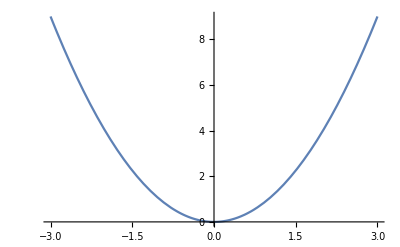

```mathematica
Plot[x^2,{x,-3,3}]
```

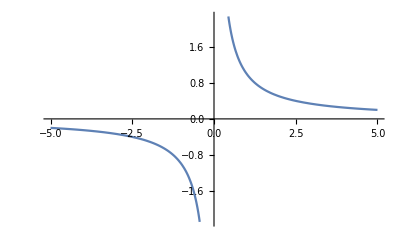

```mathematica
Plot[1/x,{x,-5,5}]
```

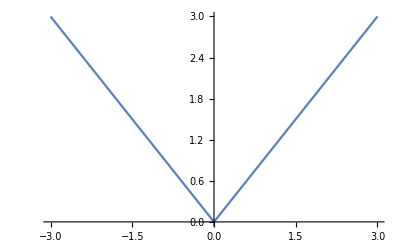

```mathematica
Plot[Abs[x],{x,-3,3}]
```

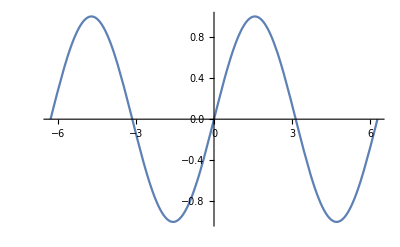

```mathematica
Plot[Sin[θ],{θ,-2π,2π}]
```

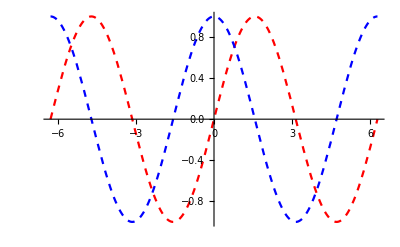

```mathematica
Plot[{Sin[θ],Cos[θ]},{θ,-2π,2π},PlotStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}]
```

```mathematica
Manipulate[Plot[x^n,{x,-3,3}],{n,1,10,1}]
```

```mathematica
Manipulate[Plot[a*x^2,{x,-3,3},PlotRange->{0,10}],{a,1,5,1}]
```

```mathematica
Manipulate[Plot[x^2+b*x,{x,-3,3},PlotRange->{-10,10}],{b,-3,3,1}]
```

```mathematica
Manipulate[Plot[x^2+c,{x,-3,3},PlotRange->{-10,10}],{c,-3,3,1}]
```

```mathematica
Manipulate[Plot[Sin[θ+ϕ],{θ,-2π,2π}],{ϕ,-2,2,0.1}]
```

```mathematica
Manipulate[Plot[a*Sin[θ],{θ,-2π,2π},PlotRange->{-5,5}],{a,-5,5}]
```

```mathematica
f[x_]:=x^2;
Plot[f[x],{x,-3,3}]
```

-Graphics-

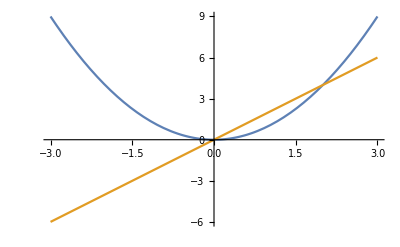

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

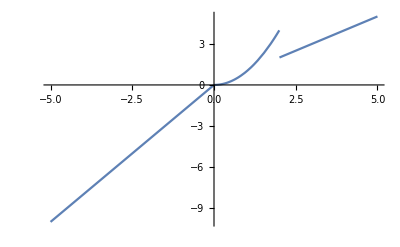

```mathematica
h[x_]:=Piecewise[{{2x, x<0}, {x^2, 0<=x<=2}, {x, x>2}}]
Plot[h[x],{x,-5,5}]
```

```mathematica
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x]+Cos[y],{x,-3,3},{y,-3,3},Mesh->None]
```

-Graphics3D-

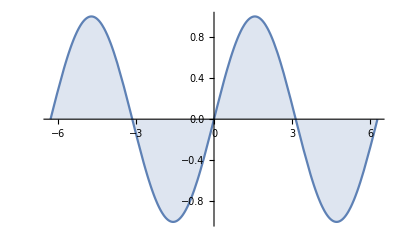

```mathematica
Plot[Sin[x],{x,-2π,2π},Filling->Axis]
```

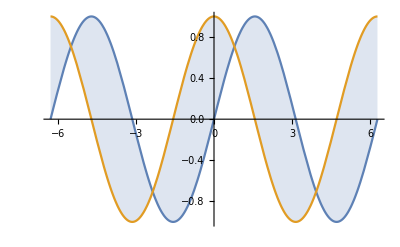

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2π,2π},Filling->{1->{2}}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2π,2π},PlotLabels->{Sin[x],Cos[x]}]
```

-Graphics-

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2π,2π},PlotLabels->{Sin[x],Cos[x]},PlotLegends->{"Sin(x)","Cos(x)"}]
```

-Graphics-

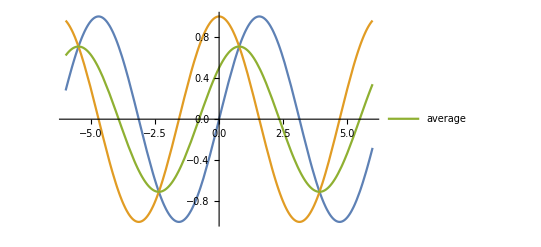

```mathematica
Plot[{Sin[x],Cos[x],Legended[Mean[{Sin[x],Cos[x]}],"average"]},{x,-6,6}]
```

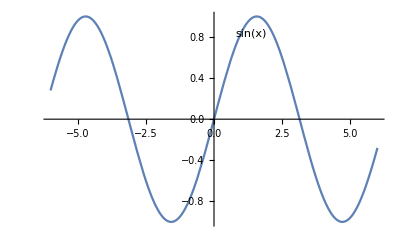

```mathematica
Plot[Labeled[Sin[x],"sin(x)",1],{x,-6,6}]
```

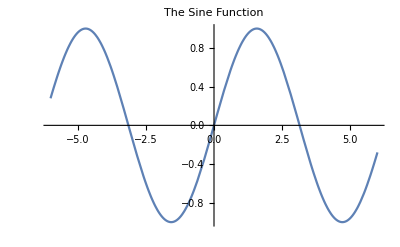

```mathematica
Plot[Sin[x],{x,-6,6},PlotLabel->"The Sine Function"]
```

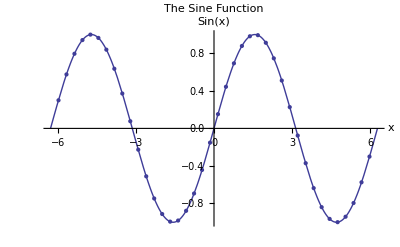

```mathematica
Plot[Sin[x],{x,-2π,2π},AxesLabel->{"x","Sin(x)"},PlotLabel->"The Sine Function",PlotTheme->"Classic",Mesh->40]
```

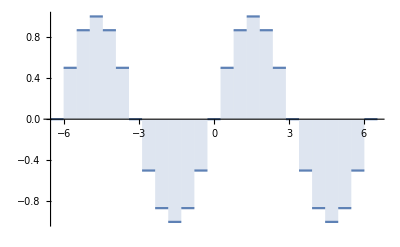

```mathematica
DiscretePlot[Sin[x],{x,-2π,2π,π/6},ExtentSize->Full]
```

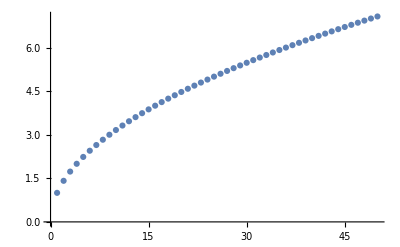

```mathematica
ListPlot[Sqrt[Range[50]]]
```

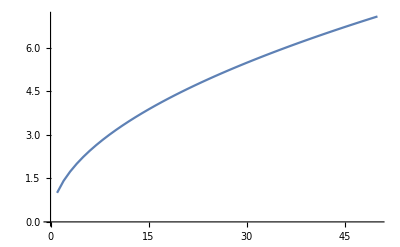

```mathematica
ListLinePlot[Sqrt[Range[50]]]
```

```mathematica
g[x_]:=x^3;
f@x_:=x^4;
```

```mathematica
f[2]
```

16

```mathematica
k@l@t
```

k[l[t]]

```mathematica
clear[f]
```

clear[f]

```mathematica
x//f
```

x^4

```mathematica
Clear[f]
```

```mathematica
x//f
```

f[x]

```mathematica
{x,y}//j//h//f
```

f[h[j[{x,y}]]]

```mathematica
f/@{a,b,c}
```

{f[a],f[b],f[c]}

```mathematica
Map[t,{x,y,z}]
```

{t[x],t[y],t[z]}

# Replace operator

```mathematica
f@{a,b,c}
```

f[{a,b,c}]

```mathematica
f@a+f@b/.f[x_]->x^3
```

a^3+b^3

```mathematica
Log[a*b]
```

Log[a b]

```mathematica
logRule={Log[a_*b_]->Log[a]+Log[b],Log[c_^d_]->d*Log[c],Log[p_/q_]->Log[p]-Log[q]}
```

{Log[a_ b_]→Log[a]+Log[b],Log[c_^d_]→d Log[c],Log[p_/q_]→Log[p]-Log[q]}

```mathematica
Log[x*y]/.logRule
```

Log[x]+Log[y]

```mathematica
Log[x^2]/.logRule
```

2 Log[x]

```mathematica
mySort={l___,x_,y_,m____}/;!OrderedQ[{x,y}]->{l,y,x,m};
```

```mathematica
{2,4,3,5,6,3,4,5,2,1,2,3}//.mySort
```

{2,4,3,5,6,3,4,5,2,1,2,3}

```mathematica
functionList={f[1],f[2]};
```

```mathematica
functionList/.f[x_]->f[RandomReal[]]
```

{f[0.933515],f[0.933515]}

# Working with datas

```mathematica
Import["Exampledata/numberdata.csv"]
```

{{1.2,4.5,6.7},{5.4,1.,0.},{0.,2.1,3.1}}

```mathematica
dataset=Dataset[{<|"a"->1,"b"->2,"c"->3|>,<|"a"->3,"b"->3,"c"->4|>,<|"a"->-1,"b"->0,"c"->3|>}]
```

```mathematica
NotebookDirectory[]
```

D:\DEBADES SIR;S PAPERS\

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\DEBADES SIR;S PAPERS

```mathematica
data=SemanticImport["Comorbid.csv"]
```

SemanticImport::nffil: File not found during SemanticImport.

$Failed

```mathematica
dataset[[1]]
```

```mathematica
dataset[[2]]
```

```mathematica
dataset[[2,All]]
```

```mathematica
dataset[[2,"c"]]
```

4

```mathematica
dataset[[{1,3},All]]
```